Pregunta 1

Parte a

```mathematica
Clear[alfa,beta,s1,s2,x,y,z,plot1,Lc];
alfa = 4;
beta = 9;
s1 = z-2-x-beta;
s2 = 4z -x^2-(y-alfa)^2;
s3 = y-alfa;

plot1 = ContourPlot3D[{s1,s2},{x,-15,15},{y,-15,15},{z,0,20},Contours->{0},ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]],Mesh->None,BoundaryStyle->{1->None,2->None,{1,2}->{{Blue,Tube[.1]}}},ViewPoint->{-15,20,25}];

z1=Solve[s1==0,z];
interseccion= s2*(-1)/.z1[[1]]//Together;

interseccion == (x-2)^2+(y-4)^2-48
Expand[%]
interseccion = (x-2)^2/(√48)^2+(y-4)^2/(√48)^2==1;

f1 ={2+√48 Cos[t],2+√48 Sin[t],2+2+√48 Cos[t]+beta};
ParametricPlot3D[f1,{t,0,2Pi}]
plot1

Lc=Integrate[Sqrt[D[f1[[1]],t]^2+D[f1[[2]],t]^2+D[f1[[3]],t]^2],{t,0,2Pi}]//N
```

-28-4 x+x^2-8 y+y^2==-48+(-2+x)^2+(-4+y)^2

True

-Graphics3D-

-Graphics3D-

52.9342

Parte b

```mathematica
Clear[densidad,Lm];

densidad =x^2+y^2+z^2;
densidad= densidad/.{{x->2+√48 Cos[t],y->2+√48 Sin[t],z->2+2+√48 Cos[t]+beta}}[[1]] //FullSimplify

Lm=Integrate[densidad*Sqrt[D[f1[[1]],t]^2+D[f1[[2]],t]^2+D[f1[[3]],t]^2],{t,0,2Pi}]//N
```

249+120 √3 Cos[t]+24 Cos[2 t]+16 √3 Sin[t]

13072.8

Pregunta 2

Parte a

```mathematica
Clear[x,y,z,f,F,g,h];
F={x*g[x^2+y^2],y*g[x^2+y^2],0};
f=1/2∫_a^(x^2+y^2) g[t]ⅆt;
gradf = Grad[f,{x,y,z}]
gradf==F
```

{x g[x^2+y^2],y g[x^2+y^2],0}

True

Parte b

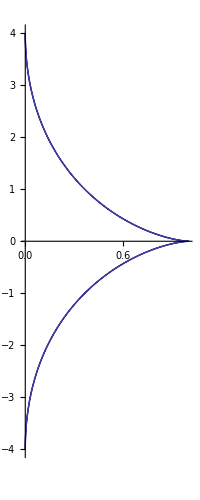

x (x^2+y^2)^(-3-alfa) ⅆx+y (x^2+y^2)^(-3-alfa) ⅆy

0

0.0000119054

```mathematica
Clear[x,y,f,int];
ParametricPlot[{(Cos[t])^4,4(Sin[t])^3},{t,0,2Pi}]
int = xⅆx/((x^2+y^2)^(alfa+3))+yⅆy/((x^2+y^2)^(alfa+3))
f[t_]=(-4(Cos[t])^4(Sin[t])^3)/(Cos[t]^8+16 Sin[t]^6)^7+(4*12(Cos[t])^2(Sin[t])^3)/(Cos[t]^8+16 Sin[t]^6)^7;
(2Pi)/6(f[0]+4f[Pi]+f[2Pi])
```

Pregunta 3